## Exclusion and reach plots for our RPV SUSY model with the jet mass cut analysis at 14 TeV, 300 and 3000 fb^-1

### Import the raw mothersets

```mathematica
SetDirectory[NotebookDirectory[]];
SignalMotherSet=Import["Results/JetMassCut_signals_14TeV.dat"];
BackgroundMotherSet=Import["Results/JetMassCut_backgrounds_14TeV.dat"];
```

### Separate the data into runs

```mathematica
SignalRuns=Partition[SignalMotherSet,45];
BackgroundRuns=Partition[BackgroundMotherSet,45];
```

### Combine backgrounds

Combine the ttbarW and ttbarZ runs separately

```mathematica
CombineBackgroundRuns[BackgroundType_,Runs_]:=Module[{RunSet,ResultRun,iRun,N1,N2,WeightedAverage,iRow},
RunSet=Select[Runs,StringSplit[#[[2,1]],"_"][[1]]==BackgroundType&];
ResultRun=RunSet[[1]];
ResultRun[[2]]={BackgroundType,""};

For[iRun=2,iRun≤Length[RunSet],iRun++,
N1=ResultRun[[4,4]];
N2=RunSet[[iRun,4,4]];
WeightedAverage[V1_,V2_]:=(N1*V1+N2*V2)/(N1+N2);

ResultRun[[4,1]]=WeightedAverage[ResultRun[[4,1]],RunSet[[iRun,4,1]]];
ResultRun[[4,3]]=WeightedAverage[ResultRun[[4,3]],RunSet[[iRun,4,3]]];
ResultRun[[4,4]]+=N2;

For[iRow=6,iRow≤6+8,iRow++,
ResultRun[[iRow,2]]+=RunSet[[iRun,iRow,2]];
ResultRun[[iRow,3]]=WeightedAverage[ResultRun[[iRow,3]],RunSet[[iRun,iRow,3]]];
ResultRun[[iRow,4]]+=RunSet[[iRun,iRow,4]];
ResultRun[[iRow,5]]=WeightedAverage[ResultRun[[iRow,5]],RunSet[[iRun,iRow,5]]];
ResultRun[[iRow,6]]+=RunSet[[iRun,iRow,6]];
ResultRun[[iRow,7]]=WeightedAverage[ResultRun[[iRow,7]],RunSet[[iRun,iRow,7]]];
ResultRun[[iRow,8]]+=RunSet[[iRun,iRow,8]];
ResultRun[[iRow,9]]=WeightedAverage[ResultRun[[iRow,9]],RunSet[[iRun,iRow,9]]];
ResultRun[[iRow,10]]+=RunSet[[iRun,iRow,10]];
ResultRun[[iRow,11]]=WeightedAverage[ResultRun[[iRow,11]],RunSet[[iRun,iRow,11]]];
];

For[iRow=16,iRow≤16+8,iRow++,
ResultRun[[iRow,2]]+=RunSet[[iRun,iRow,2]];
ResultRun[[iRow,3]]=WeightedAverage[ResultRun[[iRow,3]],RunSet[[iRun,iRow,3]]];
ResultRun[[iRow,4]]=WeightedAverage[ResultRun[[iRow,4]],RunSet[[iRun,iRow,4]]];
ResultRun[[iRow,5]]=WeightedAverage[ResultRun[[iRow,5]],RunSet[[iRun,iRow,5]]];
ResultRun[[iRow,6]]=WeightedAverage[ResultRun[[iRow,6]],RunSet[[iRun,iRow,6]]];
];

For[iRow=26,iRow≤26+8,iRow++,
ResultRun[[iRow,2]]+=RunSet[[iRun,iRow,2]];
ResultRun[[iRow,3]]=WeightedAverage[ResultRun[[iRow,3]],RunSet[[iRun,iRow,3]]];
ResultRun[[iRow,4]]=WeightedAverage[ResultRun[[iRow,4]],RunSet[[iRun,iRow,4]]];
ResultRun[[iRow,5]]=WeightedAverage[ResultRun[[iRow,5]],RunSet[[iRun,iRow,5]]];
ResultRun[[iRow,6]]=WeightedAverage[ResultRun[[iRow,6]],RunSet[[iRun,iRow,6]]];
ResultRun[[iRow,7]]=WeightedAverage[ResultRun[[iRow,7]],RunSet[[iRun,iRow,7]]];
];

For[iRow=36,iRow≤36+8,iRow++,
ResultRun[[iRow,2]]+=RunSet[[iRun,iRow,2]];
ResultRun[[iRow,3]]=WeightedAverage[ResultRun[[iRow,3]],RunSet[[iRun,iRow,3]]];
ResultRun[[iRow,4]]=WeightedAverage[ResultRun[[iRow,4]],RunSet[[iRun,iRow,4]]];
ResultRun[[iRow,5]]=WeightedAverage[ResultRun[[iRow,5]],RunSet[[iRun,iRow,5]]];
ResultRun[[iRow,6]]=WeightedAverage[ResultRun[[iRow,6]],RunSet[[iRun,iRow,6]]];
ResultRun[[iRow,7]]=WeightedAverage[ResultRun[[iRow,7]],RunSet[[iRun,iRow,7]]];
];
];

Return[ResultRun];
];

ttbarWRun=CombineBackgroundRuns["ttbarW",BackgroundRuns];
ttbarZRun=CombineBackgroundRuns["ttbarZ",BackgroundRuns];
```

### Define functions for accessing the data in each run

```mathematica
GetGluinoMass[Run_]:=ToExpression[StringSplit[Run[[2,1]],"_"][[2]]];
GetStopMass[Run_]:=ToExpression[StringSplit[Run[[2,1]],"_"][[3]]];

GetNumEvents[Run_,SR_,NHMJ_,Lumi_]:=Run[[16+NHMJ*10+SR,Switch[NHMJ,0,Switch[Lumi,300,5,3000,6],_,Switch[Lumi,300,6,3000,7]]]];
```

## Calculate the total background

ζ at 14 TeV estimated in /04-BoostRPVSUSY/04-NewCuts/Zeta_SUS-12-029.nb.

```mathematica
Getζ14[SR_]:={4.206726939924666,3.807148679689271,3.1101351002850475,2.090468266535269,2.7757497298896703,2.411310753126302,1.8626745862956555,3.1601270449730587,2.62412937122528}[[SR+1]];

GetBackground[SR_,NHMJ_,Lumi_]:=Getζ14[SR]*(GetNumEvents[ttbarWRun,SR,NHMJ,Lumi]+GetNumEvents[ttbarZRun,SR,NHMJ,Lumi]);
```

## Calculating the expected p-value (CLs method) and significance for a given number of signal and background events

Improved algorithm for computing the expected p-value (CLs method), developed in /07-.../01-.../ExpectedCLsPvalue.nb.

```mathematica
ExpectedPvalue[s_,b_]:=Module[{P,Psb},
P[n_,λ_]:=PDF[PoissonDistribution[λ],n];
Psb[n_,λ_]:=CDF[PoissonDistribution[λ],n];
Return[N[Sum[P[n,b]*Psb[n,s+b]/Psb[n,b],{n,0,5000}]]];
];

GetExclusionLimit[b_]:=s/.FindRoot[ExpectedPvalue[s,b]==0.05,{s,20}];
```

Note that since the sum only goes up to 5000, it may not be advised to use this for NHMJ = 0 without increasing it.  But I’ve kept it at 5000 because I don’t think I’ll be plotting that for now.

```mathematica
Significance[S_,B_]:=√(2*((S+B)*Log[1+S/B]-S));
Get5σReach[B_]:=S/.FindRoot[Significance[S,B]==5,{S,20}];
```

## 95%CL exclusion plots for 14 TeV and 300 fb^-1, 3000 fb^-1

```mathematica
Needs["PlotLegends`"];
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

### Combined plots

{L_int = 300 fb^-1:,SR# | N_HMJ | B | S_limit | S_limit/B
0 | 1 | 84.1919 | 24.3233 | 0.288902
1 | 1 | 72.3096 | 22.6909 | 0.313803
2 | 1 | 36.2311 | 16.6621 | 0.459884
3 | 1 | 4.26458 | 7.12626 | 1.67103
4 | 1 | 10.6127 | 9.98317 | 0.940684
5 | 1 | 9.2193 | 9.45047 | 1.02508
6 | 1 | 3.79988 | 6.85145 | 1.80307
8 | 1 | 12.189 | 10.5459 | 0.865201
0 | 2 | 2.02661 | 5.61495 | 2.77061
1 | 2 | 1.77182 | 5.40027 | 3.04787
2 | 2 | 0.761303 | 4.3606 | 5.72781
3 | 2 | 0.230606 | 3.5462 | 15.3778
4 | 2 | 0.397122 | 3.84273 | 9.67644
5 | 2 | 0.344982 | 3.75554 | 10.8862
6 | 2 | 0.205477 | 3.49609 | 17.0145
8 | 2 | 0.504298 | 4.00961 | 7.95087,L_int = 3000 fb^-1:,SR# | N_HMJ | B | S_limit | S_limit/B
0 | 1 | 841.919 | 72.5597 | 0.0861836
1 | 1 | 723.096 | 67.3907 | 0.0931975
2 | 1 | 362.311 | 48.2868 | 0.133275
3 | 1 | 42.6458 | 17.9017 | 0.419777
4 | 1 | 106.127 | 27.059 | 0.254969
5 | 1 | 92.193 | 25.3583 | 0.275057
6 | 1 | 37.9988 | 17.0139 | 0.447749
8 | 1 | 121.89 | 28.8536 | 0.236719
0 | 2 | 20.2661 | 12.9867 | 0.640807
1 | 2 | 17.7182 | 12.2794 | 0.693039
2 | 2 | 7.61303 | 8.78475 | 1.15391
3 | 2 | 2.30606 | 5.83651 | 2.53095
4 | 2 | 3.97122 | 6.95455 | 1.75124
5 | 2 | 3.44982 | 6.63367 | 1.9229
6 | 2 | 2.05477 | 5.6379 | 2.74381
8 | 2 | 5.04298 | 7.55616 | 1.49835}

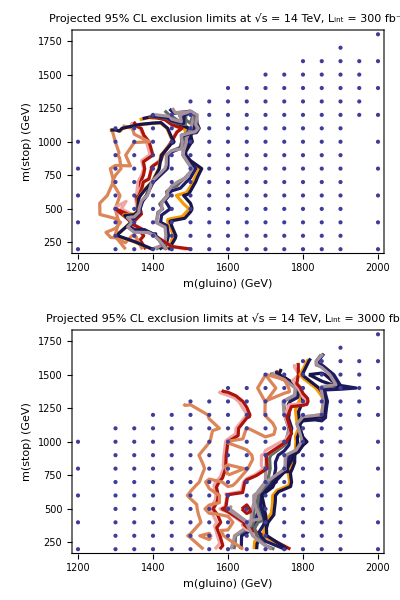

```mathematica
Module[{RangeToPlot,IntLumis,SRlabels,SRcolors,theTables,thePlotLists,iLumi,iSR,iNHMJ,B,Slimit,PointGrid},
RangeToPlot={{1200,2000},{200,1800}};
IntLumis={300,3000};
SRlabels={"SR0: H_T > 80, MET > 0","SR1: H_T > 80, MET > 30","SR2: H_T > 80, MET > 30, ++ only","SR3: H_T > 200, MET > 120","SR4: H_T > 200, MET > 50","SR5: H_T > 320, MET > 50","SR6: H_T > 320, MET > 120","(SR7 not simulated)","SR8: H_T > 320, MET > 0"};
SRcolors=ColorData[9,"ColorList"];

theTables={{{"SR#","N_HMJ","B","S_limit","S_limit/B"}},{{"SR#","N_HMJ","B","S_limit","S_limit/B"}}};
thePlotLists={{},{}};

For[iLumi=1,iLumi≤2,iLumi++,
For[iNHMJ=1,iNHMJ≤2,iNHMJ++,
For[iSR=0,iSR≤8,iSR++,
If[iSR==7,Continue[]];  (* we aren't analyzing SR7 at 14 TeV *)

B=GetBackground[iSR,iNHMJ,IntLumis[[iLumi]]];
Slimit=GetExclusionLimit[B];
AppendTo[theTables[[iLumi]],{iSR,iNHMJ,B,Slimit,N[Slimit/B]}];

AppendTo[thePlotLists[[iLumi]],ListContourPlot[{GetGluinoMass[#],GetStopMass[#],GetNumEvents[#,iSR,iNHMJ,IntLumis[[iLumi]]]}&/@SignalRuns,Contours->{Slimit},PlotRange->RangeToPlot,ContourStyle->{SRcolors[[iSR+1]],Thickness[0.004]},ContourShading->None,PlotLabel->"Projected 95% CL exclusion limits at √s = 14 TeV, L_int = "<>ToString[IntLumis[[iLumi]]]<>" fb^-1",FrameLabel->{"m(gluino) (GeV)", "m(stop) (GeV)"},ImageSize->Large,Background->White,Mesh->None]];
];
];
];

PointGrid=ListPlot[{GetGluinoMass[#],GetStopMass[#]}&/@SignalRuns,PlotRange->RangeToPlot];


Print[{"L_int = "<>ToString[IntLumis[[1]]]<>" fb^-1:",Grid[theTables[[1]],Dividers->{{False,False,True,True},{False,True}}],"L_int = "<>ToString[IntLumis[[2]]]<>" fb^-1:",Grid[theTables[[2]],Dividers->{{False,False,True,True},{False,True}}]}];

Grid[{{GraphicsRow[{Show[##,PointGrid]&@@thePlotLists[[1]],Graphics[Legend[{SRcolors[[#]],SRlabels[[#]]}&/@Range[9],LegendShadow->False,LegendTextSpace->11],ImageSize->175]},-200]},
{GraphicsRow[{Show[##,PointGrid]&@@thePlotLists[[2]],Graphics[Legend[{SRcolors[[#]],SRlabels[[#]]}&/@Range[9],LegendShadow->False,LegendTextSpace->11],ImageSize->175]},-200]}}]
]
```

### Separated by N_HMJ

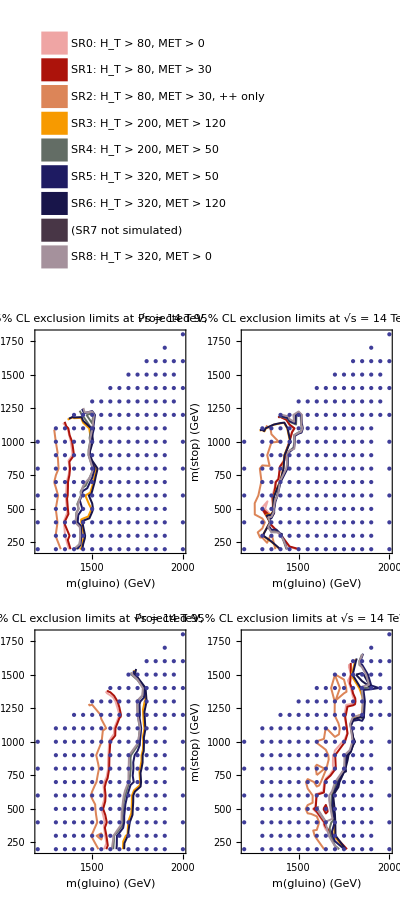

```mathematica
Module[{RangeToPlot,IntLumis,SRlabels,SRcolors,theTables,thePlotLists,iLumi,iSR,iNHMJ,B,Slimit,PointGrid},
RangeToPlot={{1200,2000},{200,1800}};
IntLumis={300,3000};
SRlabels={"SR0: H_T > 80, MET > 0","SR1: H_T > 80, MET > 30","SR2: H_T > 80, MET > 30, ++ only","SR3: H_T > 200, MET > 120","SR4: H_T > 200, MET > 50","SR5: H_T > 320, MET > 50","SR6: H_T > 320, MET > 120","(SR7 not simulated)","SR8: H_T > 320, MET > 0"};
SRcolors=ColorData[9,"ColorList"];

(*theTables={{{"SR#","N_HMJ","B","S_limit","S_limit/B"}},{{"SR#","N_HMJ","B","S_limit","S_limit/B"}}};*)
thePlotLists={{},{}};

For[iLumi=1,iLumi≤2,iLumi++,
For[iNHMJ=1,iNHMJ≤2,iNHMJ++,
AppendTo[thePlotLists[[iLumi]],{}];

For[iSR=0,iSR≤8,iSR++,
If[iSR==7,Continue[]];  (* we aren't analyzing SR7 at 14 TeV *)

B=GetBackground[iSR,iNHMJ,IntLumis[[iLumi]]];
Slimit=GetExclusionLimit[B];
(*AppendTo[theTables[[iLumi]],{iSR,iNHMJ,B,Slimit,N[Slimit/B]}];*)

AppendTo[thePlotLists[[iLumi,iNHMJ]],ListContourPlot[{GetGluinoMass[#],GetStopMass[#],GetNumEvents[#,iSR,iNHMJ,IntLumis[[iLumi]]]}&/@SignalRuns,Contours->{Slimit},PlotRange->RangeToPlot,ContourStyle->{SRcolors[[iSR+1]],Thickness[0.004]},ContourShading->None,PlotLabel->"Projected 95% CL exclusion limits at √s = 14 TeV, L_int = "<>ToString[IntLumis[[iLumi]]]<>" fb^-1",FrameLabel->{"m(gluino) (GeV)", "m(stop) (GeV)"},ImageSize->Medium,Background->White,Mesh->None]];
];
];
];

PointGrid=ListPlot[{GetGluinoMass[#],GetStopMass[#]}&/@SignalRuns,PlotRange->RangeToPlot];


(*Print[{"L_int = "<>ToString[IntLumis[[1]]]<>" fb^-1:",Grid[theTables[[1]],Dividers->{{False,False,True,True},{False,True}}],"L_int = "<>ToString[IntLumis[[2]]]<>" fb^-1:",Grid[theTables[[2]],Dividers->{{False,False,True,True},{False,True}}]}];*)

Grid[{{Graphics[Legend[{SRcolors[[#]],SRlabels[[#]]}&/@Range[9],LegendShadow->False,LegendTextSpace->11],ImageSize->175]},
{GraphicsRow[{Show[##,PointGrid]&@@thePlotLists[[1,1]],Show[##,PointGrid]&@@thePlotLists[[1,2]]}]},
{GraphicsRow[{Show[##,PointGrid]&@@thePlotLists[[2,1]],Show[##,PointGrid]&@@thePlotLists[[2,2]]}]}}]
]
```

## 5σ reach plots for 14 TeV and 300 fb^-1, 3000 fb^-1

```mathematica
Needs["PlotLegends`"];
```

### Combined plots

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{L_int = 300 fb^-1:,SR# | N_HMJ | B | S_(5  σ) | S_(5  σ)/B
0 | 1 | 84.1919 | 49.8786 | 0.59244
1 | 1 | 72.3096 | 46.5066 | 0.643159
2 | 1 | 36.2311 | 34.024 | 0.939083
3 | 1 | 4.26458 | 13.9532 | 3.27188
4 | 1 | 10.6127 | 20.066 | 1.89076
5 | 1 | 9.2193 | 18.9381 | 2.05419
6 | 1 | 3.79988 | 13.3532 | 3.5141
8 | 1 | 12.189 | 21.2537 | 1.74368
0 | 2 | 2.02661 | 10.6002 | 5.2305
1 | 2 | 1.77182 | 10.1094 | 5.70566
2 | 2 | 0.761303 | 7.62648 | 10.0177
3 | 2 | 0.230606 | 5.37141 | 23.2926
4 | 2 | 0.397122 | 6.25725 | 15.7565
5 | 2 | 0.344982 | 6.0082 | 17.416
6 | 2 | 0.205477 | 5.20764 | 25.3441
8 | 2 | 0.504298 | 6.71573 | 13.317,L_int = 3000 fb^-1:,SR# | N_HMJ | B | S_(5  σ) | S_(5  σ)/B
0 | 1 | 841.919 | 149.189 | 0.177201
1 | 1 | 723.096 | 138.557 | 0.191617
2 | 1 | 362.311 | 99.2537 | 0.273946
3 | 1 | 42.6458 | 36.5956 | 0.858129
4 | 1 | 106.127 | 55.5257 | 0.523202
5 | 1 | 92.193 | 52.0157 | 0.564204
6 | 1 | 37.9988 | 34.7542 | 0.914613
8 | 1 | 121.89 | 59.2276 | 0.485912
0 | 2 | 20.2661 | 26.3728 | 1.30132
1 | 2 | 17.7182 | 24.8937 | 1.40498
2 | 2 | 7.61303 | 17.5226 | 2.30166
3 | 2 | 2.30606 | 11.1018 | 4.81417
4 | 2 | 3.97122 | 13.5787 | 3.41927
5 | 2 | 3.44982 | 12.8752 | 3.73213
6 | 2 | 2.05477 | 10.6524 | 5.1842
8 | 2 | 5.04298 | 14.886 | 2.95183}

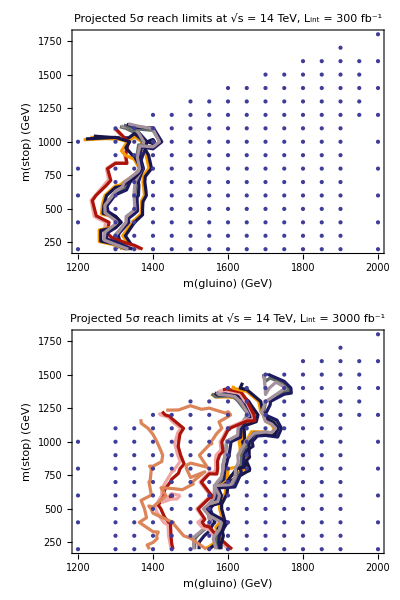

```mathematica
Module[{RangeToPlot,IntLumis,SRlabels,SRcolors,theTables,thePlotLists,iLumi,iSR,iNHMJ,B,Sreach,PointGrid},RangeToPlot={{1200,2000},{200,1800}};
IntLumis={300,3000};
SRlabels={"SR0: H_T > 80, MET > 0","SR1: H_T > 80, MET > 30","SR2: H_T > 80, MET > 30, ++ only","SR3: H_T > 200, MET > 120","SR4: H_T > 200, MET > 50","SR5: H_T > 320, MET > 50","SR6: H_T > 320, MET > 120","(SR7 not simulated)","SR8: H_T > 320, MET > 0"};
SRcolors=ColorData[9,"ColorList"];

theTables={{{"SR#","N_HMJ","B","S_(5  σ)","S_(5  σ)/B"}},{{"SR#","N_HMJ","B","S_(5  σ)","S_(5  σ)/B"}}};
thePlotLists={{},{}};

For[iLumi=1,iLumi≤2,iLumi++,
For[iNHMJ=1,iNHMJ≤2,iNHMJ++,
For[iSR=0,iSR≤8,iSR++,
If[iSR==7,Continue[]];  (* we aren't analyzing SR7 at 14 TeV *)

B=GetBackground[iSR,iNHMJ,IntLumis[[iLumi]]];
Sreach=Get5σReach[B];
AppendTo[theTables[[iLumi]],{iSR,iNHMJ,B,Sreach,N[Sreach/B]}];

AppendTo[thePlotLists[[iLumi]],ListContourPlot[{GetGluinoMass[#],GetStopMass[#],GetNumEvents[#,iSR,iNHMJ,IntLumis[[iLumi]]]}&/@SignalRuns,Contours->{Sreach},PlotRange->RangeToPlot,ContourStyle->{SRcolors[[iSR+1]],Thickness[0.004]},ContourShading->None,PlotLabel->"Projected 5σ reach limits at √s = 14 TeV, L_int = "<>ToString[IntLumis[[iLumi]]]<>" fb^-1",FrameLabel->{"m(gluino) (GeV)", "m(stop) (GeV)"},ImageSize->Large,Background->White,Mesh->None]];
];
];
];

PointGrid=ListPlot[{GetGluinoMass[#],GetStopMass[#]}&/@SignalRuns,PlotRange->RangeToPlot];


Print[{"L_int = "<>ToString[IntLumis[[1]]]<>" fb^-1:",Grid[theTables[[1]],Dividers->{{False,False,True,True},{False,True}}],"L_int = "<>ToString[IntLumis[[2]]]<>" fb^-1:",Grid[theTables[[2]],Dividers->{{False,False,True,True},{False,True}}]}];

Grid[{{GraphicsRow[{Show[##,PointGrid]&@@thePlotLists[[1]],Graphics[Legend[{SRcolors[[#]],SRlabels[[#]]}&/@Range[9],LegendShadow->False,LegendTextSpace->11],ImageSize->175]},-200]},
{GraphicsRow[{Show[##,PointGrid]&@@thePlotLists[[2]],Graphics[Legend[{SRcolors[[#]],SRlabels[[#]]}&/@Range[9],LegendShadow->False,LegendTextSpace->11],ImageSize->175]},-200]}}]
]
```

### Separated by N_HMJ

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

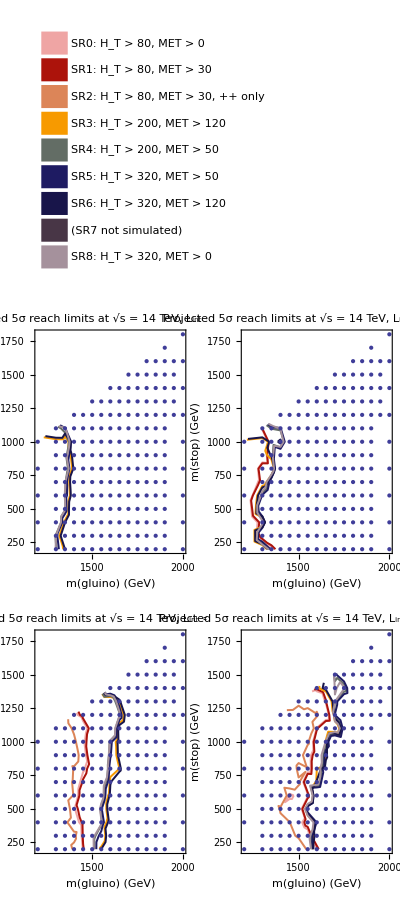

```mathematica
Module[{RangeToPlot,IntLumis,SRlabels,SRcolors,theTables,thePlotLists,iLumi,iSR,iNHMJ,B,Sreach,PointGrid},RangeToPlot={{1200,2000},{200,1800}};
IntLumis={300,3000};
SRlabels={"SR0: H_T > 80, MET > 0","SR1: H_T > 80, MET > 30","SR2: H_T > 80, MET > 30, ++ only","SR3: H_T > 200, MET > 120","SR4: H_T > 200, MET > 50","SR5: H_T > 320, MET > 50","SR6: H_T > 320, MET > 120","(SR7 not simulated)","SR8: H_T > 320, MET > 0"};
SRcolors=ColorData[9,"ColorList"];

(*theTables={{{"SR#","N_HMJ","B","S_(5 σ)","S_(5 σ)/B"}},{{"SR#","N_HMJ","B","S_(5 σ)","S_(5 σ)/B"}}};*)
thePlotLists={{},{}};

For[iLumi=1,iLumi≤2,iLumi++,
For[iNHMJ=1,iNHMJ≤2,iNHMJ++,
AppendTo[thePlotLists[[iLumi]],{}];

For[iSR=0,iSR≤8,iSR++,
If[iSR==7,Continue[]];  (* we aren't analyzing SR7 at 14 TeV *)

B=GetBackground[iSR,iNHMJ,IntLumis[[iLumi]]];
Sreach=Get5σReach[B];
(*AppendTo[theTables[[iLumi]],{iSR,iNHMJ,B,Sreach,N[Sreach/B]}];*)

AppendTo[thePlotLists[[iLumi,iNHMJ]],ListContourPlot[{GetGluinoMass[#],GetStopMass[#],GetNumEvents[#,iSR,iNHMJ,IntLumis[[iLumi]]]}&/@SignalRuns,Contours->{Sreach},PlotRange->RangeToPlot,ContourStyle->{SRcolors[[iSR+1]],Thickness[0.004]},ContourShading->None,PlotLabel->"Projected 5σ reach limits at √s = 14 TeV, L_int = "<>ToString[IntLumis[[iLumi]]]<>" fb^-1",FrameLabel->{"m(gluino) (GeV)", "m(stop) (GeV)"},ImageSize->Medium,Background->White,Mesh->None]];
];
];
];

PointGrid=ListPlot[{GetGluinoMass[#],GetStopMass[#]}&/@SignalRuns,PlotRange->RangeToPlot];


(*Print[{"L_int = "<>ToString[IntLumis[[1]]]<>" fb^-1:",Grid[theTables[[1]],Dividers->{{False,False,True,True},{False,True}}],"L_int = "<>ToString[IntLumis[[2]]]<>" fb^-1:",Grid[theTables[[2]],Dividers->{{False,False,True,True},{False,True}}]}];*)


Grid[{{Graphics[Legend[{SRcolors[[#]],SRlabels[[#]]}&/@Range[9],LegendShadow->False,LegendTextSpace->11],ImageSize->175]},
{GraphicsRow[{Show[##,PointGrid]&@@thePlotLists[[1,1]],Show[##,PointGrid]&@@thePlotLists[[1,2]]}]},
{GraphicsRow[{Show[##,PointGrid]&@@thePlotLists[[2,1]],Show[##,PointGrid]&@@thePlotLists[[2,2]]}]}}]
]
```

## Selected 5σ reach contours for the paper (PRELIMINARY)

```mathematica
Needs["PlotLegends`"];
```

### Preliminary plot 1

I’ve narrowed it down to these two: (SR, N_HMJ) = (6,1) and (5,2), for both 300 and 3000 fb^-1.  It’s hard to pick between them.

(5,2) has slightly better reach in the high stop mass region, because of the accidental substructure jets and because it requires less MET from the softer neutrinos.

SR# | N_HMJ | L_int | B | S_(5  σ) | S_(5  σ)/B
6 | 1 | 300 | 3.79988 | 13.3532 | 3.5141
5 | 2 | 300 | 0.344982 | 6.0082 | 17.416
6 | 1 | 3000 | 37.9988 | 34.7542 | 0.914613
5 | 2 | 3000 | 3.44982 | 12.8752 | 3.73213

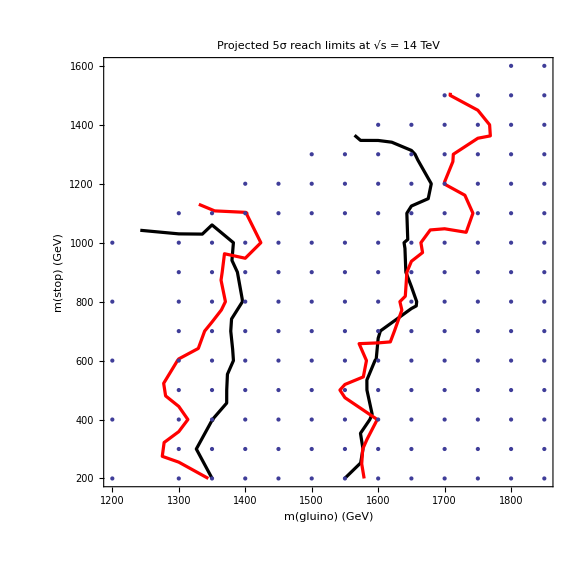

```mathematica
Module[{RangeToPlot,ContoursToPlot,theTable,thePlotList,iContour,iSR,iNHMJ,iIntLumi,iContourStyle,B,Sreach,PointGrid},
RangeToPlot={{1200,1850},{200,1600}};
ContoursToPlot={{6,1,300,{Black,Thickness[0.004]}},{5,2,300,{Red,Thickness[0.004]}},{6,1,3000,{Black,Thickness[0.004]}},{5,2,3000,{Red,Thickness[0.004]}}};

theTable={{"SR#","N_HMJ","L_int","B","S_(5  σ)","S_(5  σ)/B"}};
thePlotList={};

For[iContour=1,iContour≤Length[ContoursToPlot],iContour++,
iSR=ContoursToPlot[[iContour,1]];
iNHMJ=ContoursToPlot[[iContour,2]];
iIntLumi=ContoursToPlot[[iContour,3]];
iContourStyle=ContoursToPlot[[iContour,4]];

B=GetBackground[iSR,iNHMJ,iIntLumi];
Sreach=Get5σReach[B];
AppendTo[theTable,{iSR,iNHMJ,iIntLumi,B,Sreach,N[Sreach/B]}];

AppendTo[thePlotList,
ListContourPlot[{GetGluinoMass[#],GetStopMass[#],GetNumEvents[#,iSR,iNHMJ,iIntLumi]}&/@SignalRuns,Contours->{Sreach},PlotRange->RangeToPlot,ContourStyle->iContourStyle,ContourShading->None,PlotLabel->"Projected 5σ reach limits at √s = 14 TeV",FrameLabel->{"m(gluino) (GeV)", "m(stop) (GeV)"},ImageSize->Large,Background->White,Mesh->None]];
];

PointGrid=ListPlot[{GetGluinoMass[#],GetStopMass[#]}&/@SignalRuns,PlotRange->RangeToPlot];


Print[Grid[theTable,Dividers->{{False,False,True,True,True},{False,True}}]];

Show[##,PointGrid]&@@thePlotList
]
```

### Preliminary plot 2

(6,1) at 300 fb^-1, and (5,2) at 3000 fb^-1.

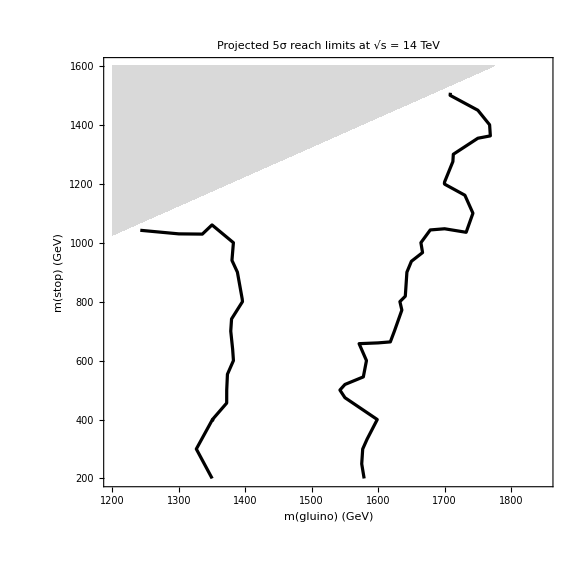

```mathematica
Module[{RangeToPlot,ContoursToPlot,theTable,thePlotList,iContour,iSR,iNHMJ,iIntLumi,iContourStyle,B,Sreach},
RangeToPlot={{1200,1850},{200,1600}};
ContoursToPlot={{6,1,300,{Black,Thickness[0.004]}},{5,2,3000,{Black,Thickness[0.004]}}};

theTable={{"SR#","N_HMJ","L_int","B","S_(5  σ)","S_(5  σ)/B"}};
thePlotList={};

For[iContour=1,iContour≤Length[ContoursToPlot],iContour++,
iSR=ContoursToPlot[[iContour,1]];
iNHMJ=ContoursToPlot[[iContour,2]];
iIntLumi=ContoursToPlot[[iContour,3]];
iContourStyle=ContoursToPlot[[iContour,4]];

B=GetBackground[iSR,iNHMJ,iIntLumi];
Sreach=Get5σReach[B];
AppendTo[theTable,{iSR,iNHMJ,iIntLumi,B,Sreach,N[Sreach/B]}];

AppendTo[thePlotList,
ListContourPlot[{GetGluinoMass[#],GetStopMass[#],GetNumEvents[#,iSR,iNHMJ,iIntLumi]}&/@SignalRuns,Contours->{Sreach},PlotRange->RangeToPlot,ContourStyle->iContourStyle,ContourShading->None,PlotLabel->"Projected 5σ reach limits at √s = 14 TeV",FrameLabel->{"m(gluino) (GeV)", "m(stop) (GeV)"},ImageSize->Large,Background->White,Mesh->None]];
];

Show[##,
RegionPlot[y>x-175,{x,RangeToPlot[[1,1]],RangeToPlot[[1,2]]},{y,RangeToPlot[[2,1]],RangeToPlot[[2,2]]},PlotRange->RangeToPlot,BoundaryStyle->None,PlotStyle->LightGray]
]&@@thePlotList
]
```

```mathematica
Export["ReachPlotPrelim2.pdf",%]
```

ReachPlotPrelim2.pdf

### Final plot

(5,2) at 300 fb^-1, and (5,2) at 3000 fb^-1.

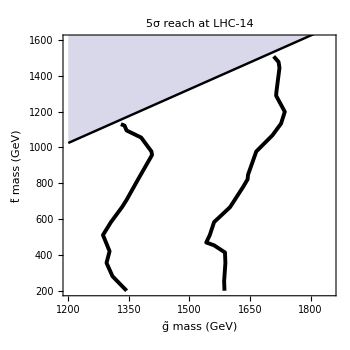

```mathematica
Module[{RangeToPlot,ContoursToPlot,theTable,thePlotList,iContour,iSR,iNHMJ,iIntLumi,iContourStyle,iReplacePoints,B,Sreach},
RangeToPlot={{1200,1850},{200,1600}};
ContoursToPlot={{5,2,300,{Black,Thickness[0.008]}},{5,2,3000,{Black,Thickness[0.008]}}};

theTable={{"SR#","N_HMJ","L_int","B","S_(5  σ)","S_(5  σ)/B"}};
thePlotList={};

For[iContour=1,iContour≤Length[ContoursToPlot],iContour++,
iSR=ContoursToPlot[[iContour,1]];
iNHMJ=ContoursToPlot[[iContour,2]];
iIntLumi=ContoursToPlot[[iContour,3]];
iContourStyle=ContoursToPlot[[iContour,4]];

B=GetBackground[iSR,iNHMJ,iIntLumi];
Sreach=Get5σReach[B];
AppendTo[theTable,{iSR,iNHMJ,iIntLumi,B,Sreach,N[Sreach/B]}];

AppendTo[thePlotList,
ListContourPlot[{GetGluinoMass[#],GetStopMass[#],GetNumEvents[#,iSR,iNHMJ,iIntLumi]}&/@SignalRuns,Contours->{Sreach},PlotRange->RangeToPlot,ContourStyle->iContourStyle,Background->White,ContourShading->None,Mesh->None,PerformanceGoal->"Speed",FrameLabel->{Style["g̃ mass (GeV)",16],Style["t̃ mass (GeV)",16]},ImageMargins->2,PlotLabel->Style["5σ reach at LHC-14",16],ImageSize->350,LabelStyle->Directive[14]]];
];

Show[##,
Plot[x-175,{x,1200,1850},PlotStyle->{Black,Thickness[0.005]},Filling->Top],
Epilog->{
Text[Rotate[Style["∫ℒ = 300 fb^-1",14],60Degree],ImageScaled@{.42,.45}(*{.32,.45}*)],
Text[Rotate[Style["∫ℒ = 3000 fb^-1",14],60Degree],ImageScaled@{.76,.45}]
}
]&@@thePlotList
]
```

```mathematica
Export["Plots/ReachPlot.pdf",%]
```

Plots/ReachPlot.pdf